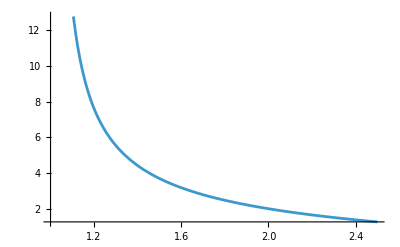

```mathematica
Plot[{x/(x-1)- Log[x-1]}, {x, 1.0, 2.5}]
```

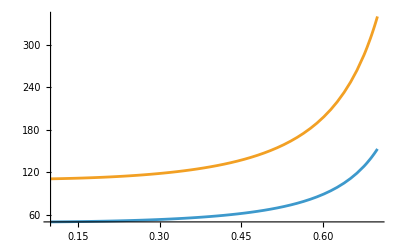

```mathematica
Plot[{Exp[3.9+(x/(1-x)+ Log[1-x])], Exp[4.7+(x/(1-x)+ Log[1-x])]}, {x, 0.1, .7}]
```

```mathematica
(1.4/0.4 - Log2[0.4])
```

4.82193

```mathematica
2.0*Log2[10] - (0.55/0.45 + Log2[0.45])
```

6.57364

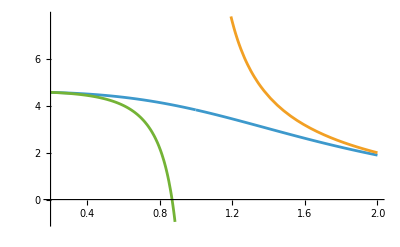

```mathematica
Plot[{-x(-(100^(1-x)Log[100])/(100^(1-x)-1) + 1/(1-x))+ Log[(100^(1-x)-1)/(1-x)], x/(x-1)- Log[x-1], Log[100]-(x/(1-x)+ Log[1-x])}, {x, 0.2, 2}]
```

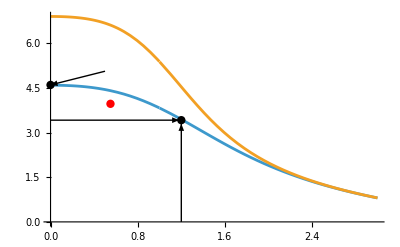

```mathematica
Plot[{
-x(-(100^(1-x)Log[100])/(100^(1-x)-1) + 1/(1-x))+ Log[(100^(1-x)-1)/(1-x)],
-x(-(1000^(1-x)Log[1000])/(1000^(1-x)-1) + 1/(1-x))+ Log[(1000^(1-x)-1)/(1-x)],
}, {x, 0.0, 3.0},
Epilog->{{Black, Arrow[{{0.0,3.42},{1.18,3.42}}] },{Black, Arrow[{{1.2,0.0},{1.2,3.3}}] },
{Black,PointSize[0.015], Point[{1.2, 3.42}]},
{Red,PointSize[0.015], Point[{0.55, 3.97}]},
{Black,PointSize[0.015], Point[{0.0, Log[100]}]},
{Black, Arrow[{{0.5,1.1*Log[100]},{0.0,Log[100]}}] }}]
```

```mathematica
{Black,PointSize[0.015], Point[{1.2, 3.42}]},
```

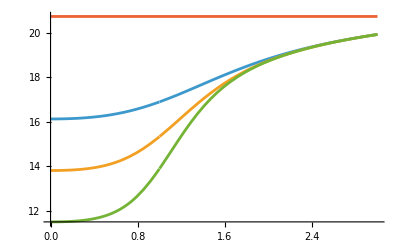

```mathematica
Plot[{
Log[10^9] - (-x(-(100^(1-x)Log[100])/(100^(1-x)-1) + 1/(1-x))+ Log[(100^(1-x)-1)/(1-x)]),
Log[10^9] - (-x(-(1000^(1-x)Log[1000])/(1000^(1-x)-1) + 1/(1-x))+ Log[(1000^(1-x)-1)/(1-x)]),
Log[10^9] - (-x(-(10000^(1-x)Log[10000])/(10000^(1-x)-1) + 1/(1-x))+ Log[(10000^(1-x)-1)/(1-x)]),
Log[10^9]}, {x, 0.0, 3}]
```

```mathematica
Log[10.^9/10^4] + (0.55/0.45 - Log[4.5])
```

11.2311

```mathematica
Log[10.^9] - (1.2/0.2 - Log[0.2])
```

13.1138

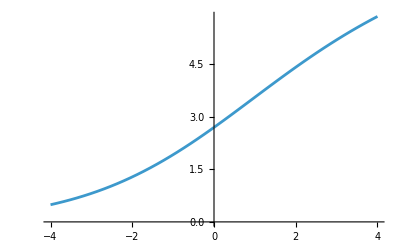

```mathematica
Plot[{Log[(x/10)*(Exp[10]-1)/(1-Exp[-x])] - (1+10/x)(1-x/(Exp[x]-1))}, {x, -4, 4}]
```

```mathematica
Manipulate[Plot[{(Log[(x-1)*(Exp[2.5*E]-1)/(1-Exp[-(2.5*(x-1)*E)])] - (x/(x-1))(1-(2.5*(x-1)*E)/(Exp[(2.5*(x-1)*E)]-1)))/Log[(2.5*10^9)/(Exp[2.5*E]-1)]}, {x, 0, 2}, PlotRange->{Automatic, {0, 1}}], {E, 0.1, 4}]
```